```mathematica
f[omega_,Omega_, t_]:= [((2*omega*Sin[2*omega *t]*Cos[Omega * t] - Omega*Cos[2 *omega*t]*Sin[Omega*t])/(4*omega^2-Omega^2))^2 + ((2*omega - Omega*Sin[2*omega*t]*Sin[Omega*t]-2*omega*Cos[2*omega*t]*Cos[Omega*t])/(4*omega^2-Omega^2))^2]
```

```mathematica
prob[omega_,Omega_,t_]:=(1/omega)^2*Abs[Integrate[Exp[2*I*omega*x]*Cos[Omega*x],{x,0,t}]]^2
```

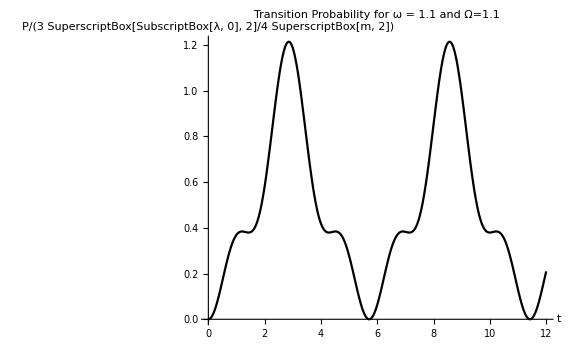

```mathematica
Plot[prob[1.1,1.1,t],{t,0,12}, PlotStyle->Black, PlotLabel->"Transition Probability for ω = 1.1 and Ω=1.1", AxesLabel->{"t", "P/(3 SuperscriptBox[SubscriptBox[λ, 0], 2]/4 SuperscriptBox[m, 2])"}, ImageSize->Large]
```

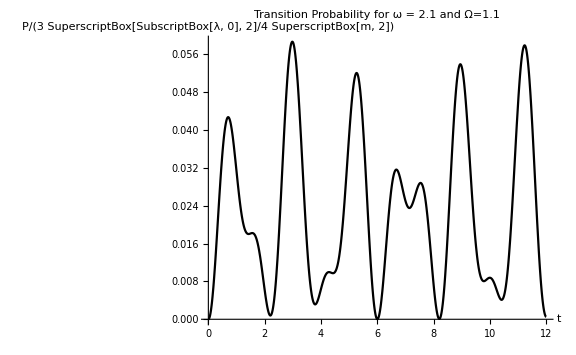

```mathematica
Plot[prob[2.1,1.1,t],{t,0,12}, PlotStyle->Black, PlotLabel->"Transition Probability for ω = 2.1 and Ω=1.1", AxesLabel->{"t", "P/(3 SuperscriptBox[SubscriptBox[λ, 0], 2]/4 SuperscriptBox[m, 2])"}, ImageSize->Large]
```